```mathematica
(* Copyright 2013 Thomas Trogdon *)
(* This software is distributed under the terms of the GNU General Public License *)
```

```mathematica
AppendTo[$Path,NotebookDirectory[]];
<<RiemannHilbert`;
<<ISTPackage`;
<<ISTPackage`mKdV`;
```

## Normal Reflection Coefficient

{0.+1.11151 ⅈ}

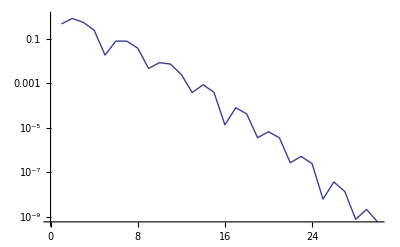
{4.40709×10^-16,-Graphics-}

```mathematica
q[x_]:=1.9 Exp[-x^2]/.Underflow[]->0/.Indeterminate->0.;
q[_?InfinityQ]:=0.
Focusing[];
LocatePolesmKdV[q,40]
H=ScatteringMatrixFinitemKdV[q,30,6];
H[_?InfinityQ]={{1,0},{0,1}};
aa//Clear;bb//Clear;
aa[k_]:=aa[k]=H[k][[1,1]];
bb[k_]:=bb[k]=H[k][[2,1]];
```

```mathematica
ν=Getnu[];
ρ[k_]:=bb[k]/aa[k];
SetScatteringData[aa,bb,ρ,LocatePolesmKdV[q,40]]
SetParams[.4,.1,10.^(-9),10,20];
h[k_]:=3/(1+Abs[k/2+1/3.2]^8);
Setrsamp[h];
Settimeflag[False];
```

## Cauchy Integral Reflection Coefficient

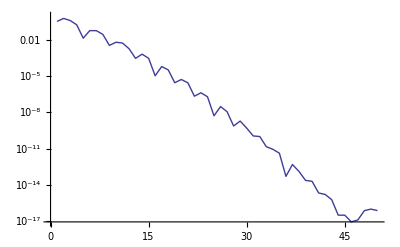
{3.71124×10^-16,-Graphics-}

```mathematica
q[x_]:=1.6Exp[-x^2]/.Underflow[]->0/.Indeterminate->0.;
q[_?InfinityQ]:=0.
Defocusing[];
LocatePolesmKdV[q,40];
H=ScatteringMatrixFinitemKdV[q,50,6];
aa//Clear;bb//Clear;
aa[k_]:=aa[k]=H[k][[1,1]];
bb[k_]:=bb[k]=H[k][[2,1]];

SetParams[.4,.1,10.^(-9),10,20];
h[k_]:=3/(1+Abs[k/2+1/3.2]^8);
Setrsamp[h];
Settimeflag[False];
ν=Getnu[];
ρ[k_]:=bb[k]/aa[k];
```

```mathematica
up=I(ν+.0001);m=50;el=8;
f={Fun[ρ,Line[{-el,0}-up],2m],Fun[ρ,Line[{0,el}-up],2m],Fun[ρ,Line[{el,0}+up],m],Fun[ρ,Line[{0,-el}+up],m]};
```

```mathematica
mρ//Clear;
mρ[k_]:=mρ[k]=Piecewise[{{Cauchy[f,k], Im[k]< Im[up]}, {ρ[k], True}}];
SetScatteringData[aa,bb,mρ,LocatePolesmKdV[q,40]]

qmKdV//Clear;
qmKdV[x_,t_]:=qmKdV[x,t]=mKdVAuto[x,t];
```

## Plotting: timestring outputs relevant computation times and region information

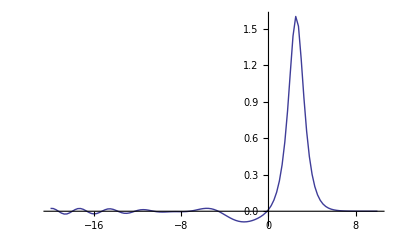

```mathematica
(* Focusing *)
Monitor[TablePlot[qmKdV[x,1.]//Re,{x,-20,10,.25},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick],timestring]
```

```mathematica
(* Defocusing *)
Monitor[TablePlot[qmKdV[x,1.]//Re,{x,-20,10,.25},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick],timestring]
```

$Aborted